## 1.feladat - szabad esés

Function[{x},-4.905 (-4.07747+1. x^2)]

2.01928

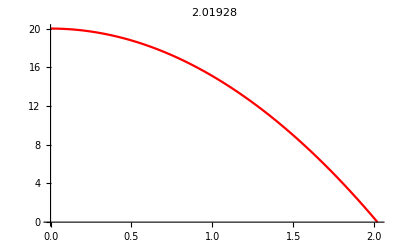

```mathematica
g=9.81;
H=20;

soly=DSolveValue[{y''[x]==-g,y'[0]==0,y[0]==H},y,x]
tmax=x/.Solve[soly[x]==0][[2]]
(*erkezes= NSolve[soly[u] == 0, {u}, Reals][[2]]*)
(*tmax= u/.erkezes*)

Plot[soly[t], {t, 0, tmax}, PlotStyle->Red,PlotLabel->tmax]
```

```mathematica
Function[{x},-4.9049999999999985 (-4.077471967380226+1. x^2)]
```

Function[{x},-4.905 (-4.07747+1. x^2)]

## 2.feladat - ferde hajlítás

```mathematica
g=9.81;
v=10;
xmag=0;
ymag=20;

solx=DSolveValue[{y''[x]==0,y[0]==xmag,y'[0]==v*Cos[Pi/4]},y,x];
soly=DSolveValue[{y''[x]==-g,y[0]==ymag,y'[0]==v*Sin[Pi/4]},y,x];
tmax=x/.Solve[{soly[x]==0,x>0},x][[1]]

Animate[
	Show[
		ParametricPlot[{solx[t],soly[t]},{t,0,tmax}, PlotStyle->{Red, Blue}, PlotLabel-> tmax],
		Graphics[  Disk[{solx[t],soly[t]},0.4]] ],
	{t,0,tmax},
	AnimationRunning->False
]
```

2.86487

## 3.feladat - matematikai inga

```mathematica
l=1;
g=9.81;
m=1;
pfi=NDSolveValue[{y''[x]==-(g/l)*Sin[y[x]],y'[0]==0,y[0]==Pi/4},y,{x,0,10}]
pendulum[fi_]:={
Line[{{0,0},{Cos[fi-Pi/2],Sin[fi-Pi/2]}}],
{Red,Disk[{Cos[fi-Pi/2],Sin[fi-Pi/2]},0.1]}};
(*Graphics[pendulum[Pi/6]]*)

Animate[
	Show[
		Graphics[{pendulum[pfi[t]]},PlotRange->{{-1.2,1.2},{-1.2,0.1}}]],
	{t,0,10},
	AnimationRunning->False
]
```

InterpolatingFunction[…]

## 4.feladat - ingamozgás kis szögek esetén

```mathematica
(*
pendulum[fi_]:={
Line[{{0,0},{Cos[fi-Pi/2],Sin[fi-Pi/2]}}],
{Red,Disk[{Cos[fi-Pi/2],Sin[fi-Pi/2]},0.1]}};
Graphics[pendulum[Pi/6]]*)
(*
Manipulate[
	pfi=NDSolveValue[{y''[x]==-(g/l)*Sin[y[x]],y'[0]==0,y[0]==alfa},y,{x,0,10}];
	pfi2=NDSolveValue[{y''[x]==-(g/l)*y[x],y'[0]==0,y[0]==alfa},y,{x,0,10}];
	Animate[
		Show[
			Graphics[{pendulum[pfi[t]],pendulum[pfi2[t]]},PlotRange->{{-1,1},{-1.2,0.1}}]],
		{t,0,10},
		AnimationRunning->False],
	{alfa,0,Pi/6}
]*)

l=1;
g=9.81;

Manipulate[
	pfi=NDSolveValue[{y''[x]==-(g/l)*Sin[y[x]],y'[0]==0,y[0]==alfa},y,{x,0,25}];
	pfi2=NDSolveValue[{y''[x]==-(g/l)*y[x],y'[0]==0,y[0]==alfa},y,{x,0,25}];
	Plot[{pfi[t],pfi2[t]},{t,0,25}],
	{alfa,0,Pi/6}
]
```

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

## 5.feladat - műküdőképes - manipulate

```mathematica
g = 9.81;
R = 1.05;
r = 0.05;

fi0=5*Pi/6;
vfi0=0;
theta0=Pi/6;
vt0=0.3;

phi=NDSolveValue[{f''[t] == (g/R)*Sin[f[t]], f[0] == fi0, f'[0]==vfi0}, f,{t,0,10}];
theta =NDSolveValue[{the''[t] == 0, the[0] == theta0, the'[0]==vt0}, the,{t,0,10}];

felgomb =  ParametricPlot3D[{R*Cos[u]*Sin[v], R*Sin[u]*Sin[v], R*Cos[v]}, {u,0,2*Pi}, {v,Pi/2,Pi}] ;

Manipulate[
palya = ParametricPlot3D[{R*Cos[theta[t]]*Sin[phi[t]], R*Sin[theta[t]]*Sin[phi[t]], R*Cos[phi[t]]}, {t,0,T}];
golyo = Graphics3D[{Red, Sphere[{R*Cos[theta[T]]*Sin[phi[T]], R*Sin[theta[T]]*Sin[phi[T]], R*Cos[phi[T]]}, r]}];
Show[felgomb,palya,golyo],
{T,1,10}
]
```

## 5. proba - működőképes - animate

```mathematica
g = 9.81;
R = 1.05;
r = 0.05;

fi0=5*Pi/6;
vfi0=0;
theta0=Pi/6;
vt0=0.3;

phi=NDSolveValue[{f''[t] == (g/R)*Sin[f[t]], f[0] == fi0, f'[0]==vfi0}, f,{t,0,10}];
theta =NDSolveValue[{the''[t] == 0, the[0] == theta0, the'[0]==vt0}, the,{t,0,10}];

felgomb =  ParametricPlot3D[{R*Cos[u]*Sin[v], R*Sin[u]*Sin[v], R*Cos[v]}, {u,0,2*Pi}, {v,Pi/2,Pi}] ;

Animate[
palya = ParametricPlot3D[{R*Cos[theta[t]]*Sin[phi[t]], R*Sin[theta[t]]*Sin[phi[t]], R*Cos[phi[t]]}, {t,0,T}];
golyo = Graphics3D[{Red, Sphere[{R*Cos[theta[T]]*Sin[phi[T]], R*Sin[theta[T]]*Sin[phi[T]], R*Cos[phi[T]]}, r]}];
Show[felgomb,palya,golyo],
{T,1,10},
AnimationRunning->False
]
```

## 5.feladat - Kész megoldás

```mathematica
g = 9.81;
R = 1.05;
r = 0.05;

phi0=5*Pi/6;
vfi0=0;
theta0=Pi/6;
vt0=0.3;

phi=NDSolveValue[{f''[t] == (g/R)*Sin[f[t]], f[0] == fi0, f'[0]==vfi0}, f,{t,0,20}]
theta =NDSolveValue[{the''[t] == 0, the[0] == theta0, the'[0]==vt0}, the,{t,0,20}]

sphericalToDescates[phi_,theta_,r_]:={r*Sin[phi]*Cos[theta],r*Sin[phi]*Sin[theta],r*Cos[phi]};

(*bowlAndBall[ido_]:=Show[
ParametricPlot3D[sphericalToDescates[phi0,theta0,1.05],{phi0,Pi/2,Pi},{theta0,0,2Pi},PlotStyle->Opacity[0.5]],
ParametricPlot3D[sphericalToDescates[phi[T],theta[T],1.05],{T,0,ido}],
Graphics3D[{Red,Sphere[sphericalToDescates[phi[ido],theta[ido],1],0.05]}],
PlotRange->{{-1.05,1.05},{-1.05,1.05},{-1.05,1.05}},Axes->True,AxesLabel->{x,y,z}];
*)

bowlAndBall[phi_,theta_]:=Show[
ParametricPlot3D[sphericalToDescates[phi0,theta0,1.05],{phi0,Pi/2,Pi},{theta0,0,2Pi},PlotStyle->Opacity[0.5]],
Graphics3D[{Red,Sphere[sphericalToDescates[phi,theta,1],0.05]}],
 PlotRange->{{-1.05,1.05},{-1.05,1.05},{-1.05,1.05}},Axes->True,AxesLabel->{x,y,z}];
(*
bowlAndBall[ido_]:=Show[
ParametricPlot3D[sphericalToDescates[phi[T],theta[T],1.05],{T,0,ido}],
Graphics3D[{Red,Sphere[sphericalToDescates[phi[ido],theta[ido],1],0.05]}],
PlotRange->{{-1.05,1.05},{-1.05,1.05},{-1.05,1.05}},Axes->True,AxesLabel->{x,y,z}];
*)

ParametricPlot3D[sphericalToDescates[phi[T],theta[T],1.05],{T,0,ido}]

Animate[
	Show[
		ParametricPlot3D[sphericalToDescates[phi[t],theta[t],1.05],{t,0,T}],
		bowlAndBall[phi[T],theta[T]],PlotRange->All],

	{T,0.1,20},
	AnimationRunning->False
]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

ParametricPlot3D::plln: Limiting value ido in {T,0,ido} is not a machine-sized real number.

ParametricPlot3D[sphericalToDescates[phi[T],theta[T],1.05],{T,0,ido}]

```mathematica
InterpolatingFunction[…]
```

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]